#### 2.1.2 | Gompertz Equation with Time Varying Injection

```mathematica
Quit[]
```

Variable Selection

```mathematica
q0=5;p0=3;k=7;α=2;d=2;
```

```mathematica
p2[t_]:= k*k^{-Exp[-α*t]}*Exp[-d*Exp[-α*(t-1)]*HeavisideTheta[t-1]]*Exp[-d*Exp[-α*(t-2)]*HeavisideTheta[t-2]]*Exp[-d*Exp[-α*(t-3)]*HeavisideTheta[t-3]]*p0^{Exp[-α*t]}
```

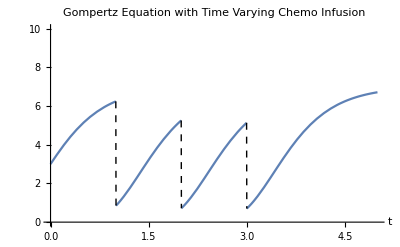

```mathematica
Plot[p2[t],{t,0,5},PlotRange->{0,10},AxesLabel->Automatic,PlotLabel->" Gompertz Equation with Time Varying Chemo Infusion",ExclusionsStyle->Dashed]
```